# Lifetime metrology

Dr Jesús Rubio
University of Surrey
j.rubiojimenez@surrey.ac.uk
ORCID iD: 0000-0002-8193-8273

Created: May 2024
Last update: July 2025

## Preamble: scale

### Prior information, symmetry function, and probe state

Prior probability:

```mathematica
Clear[θmin,θmax,p,f,ρ]
θmin[b_]=1/b;
θmax[b_]=b;
p[θ_,b_]:=Normal[1/(θ NIntegrate[1/x,{x,θmin[b],θmax[b]}])]
f[θ_]=Log[θ];
ρ[θ_]={{ Exp[- 1/θ],0},{0,1- Exp[- 1/θ]}};
```

### Prior error

```mathematica
Clear[ϵprior]
ϵprior[b_]:= NIntegrate[p[x,b] f[x]^2,{x,θmin[b],θmax[b]}]-NIntegrate[p[x,b] f[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]^2
```

### ρ_0 and ρ_1 operators

```mathematica
Clear[ρ0 ,ρ1]
ρ0[b_]:=NIntegrate[p[x,b] ρ[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]
ρ1[b_]:=NIntegrate[p[x,b] ρ[x] f[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]
```

## Preamble: geometric approach

### Symmetry function, and Jeffreys’s general rule

```mathematica
Clear[ℒ,metric,fmetric,pmetric]
ℒ[θ_]=LyapunovSolve[ρ[θ],ρ[θ],2D[ρ[θ],θ]];
metric[θ_]:=Sqrt[Tr[ρ[θ].ℒ[θ].ℒ[θ]]]
fmetric[x_?NumericQ]:=NIntegrate[metric[θ],{θ,0,x}] 
pmetric[θ_,b_]:=metric[θ]/NIntegrate[metric[x],{x,θmin[b],θmax[b]}]
```

### Prior error

```mathematica
Clear[ϵpriorMetric]
ϵpriorMetric[b_] := NIntegrate[pmetric[x,b] fmetric[x]^2,{x,θmin[b],θmax[b]}]-NIntegrate[pmetric[x,b] fmetric[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]^2;
```

### ρ_0 and ρ_1 operators

```mathematica
Clear[ρ0metric ,ρ1metric]
ρ0metric[b_]:=NIntegrate[pmetric[x,b] ρ[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]
ρ1metric[b_]:=NIntegrate[pmetric[x,b] ρ[x] fmetric[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]
```

## Intrinsic precision gain

### Scale metrology

```mathematica
Clear[εMLE]
εMLE[b_]:=(Tr[ρ1[b].LyapunovSolve[ρ0[b],2ρ1[b]]]-NIntegrate[p[x,b] f[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]^2)/ϵprior[b];
```

### Metric approach

```mathematica
Clear[εmetric]
εmetric[b_]:=(Tr[ρ1metric[b].LyapunovSolve[ρ0metric[b],2ρ1metric[b]]]-NIntegrate[pmetric[x,b] fmetric[x],{x,θmin[b],θmax[b]},AccuracyGoal->8]^2)/ϵpriorMetric[b];
```

## Plot: priors

```mathematica
Clear[ρmetricPlot,ℒplot,metricPlot]
ρmetricPlot[θ_,y_]={{y Exp[- 1/θ],Sqrt[y(1-y)] Exp[- 1/(2θ)]},{Sqrt[y(1-y)] Exp[- 1/(2θ)],1-y Exp[- 1/θ]}};
ℒplot[θ_,y_]=LyapunovSolve[ρmetricPlot[θ,y],ρmetricPlot[θ,y],2D[ρmetricPlot[θ,y],θ]];
metricPlot[θ_,y_]:=Sqrt[Tr[ρmetricPlot[θ,y].ℒplot[θ,y].ℒplot[θ,y]]]
```

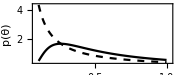

```mathematica
Clear[auxMin,auxMax,insetPriors]
auxMin=0.1;auxMax=1;
insetPriors=Plot[{1/(θ NIntegrate[1/θ,{θ,auxMin,auxMax}]),metricPlot[θ,1]/NIntegrate[metricPlot[x,1],{x,auxMin,auxMax}]},{θ,auxMin,auxMax},FrameStyle->Directive["Times",13,Black],Frame->True,PlotStyle->{{Dashed,Black},{Black},{Dashed,Black}},FrameLabel->{"θ","p(θ)"},AspectRatio->0.42,PlotRange->{{auxMin-0.025,auxMax+0.025},All},ImageSize->Small]
```

## Plot: intrinsic precision gain

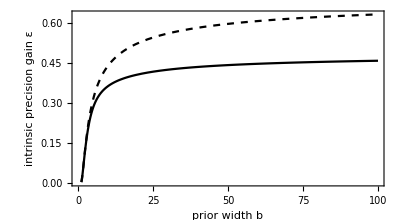

```mathematica
Plot[{εMLE[y],εmetric[y]},{y,1.1,100},FrameStyle->Directive["Times",13,Black],Frame->True,PlotStyle->{{Dashed,Black},{Black}},FrameLabel->{"prior width b","intrinsic precision gain ε"},AspectRatio->0.55,PlotRange->{Automatic,Automatic},Epilog->{Inset[insetPriors,ImageScaled[{0.72,0.45}]]}]
```

## Manuscript workings

### Analytics for information geometry

```mathematica
Clear[η,ρgeneral]
ρgeneral[θ_]={{η Exp[- 1/θ],Sqrt[η(1-η)] Exp[- 1/(2θ)]},{Sqrt[η(1-η)] Exp[- 1/(2θ)],1-η Exp[- 1/θ]}};
ℒ[θ_]=LyapunovSolve[ρgeneral[θ],ρgeneral[θ],2D[ρgeneral[θ],θ]];
Ianalytical[θ_,η_]=Tr[ρgeneral[θ].ℒ[θ].ℒ[θ]]//FullSimplify
```

(ⅇ^(-1/θ) η (-1+ⅇ^(1/θ)+η))/((-1+ⅇ^(1/θ)) θ^4)

```mathematica
(Integrate[Sqrt[Ianalytical[θ,1]],θ])^2 (* take the square root of this *)
```

4 ArcTan[√(-1+ⅇ^(1/θ))]^2

### S operator in scale metrology

```mathematica
η=1;LyapunovSolve[ρ0[10],2ρ1[10]]//MatrixForm
LyapunovSolve[ρ0metric[10],2ρ1metric[10]]//MatrixForm
Clear[η]
```

(1.08908 | 0.
0. | -0.713559)

(1.81328 | 0.
0. | 0.919513)